Main

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["hidden_soln_few_triplets.txt","Table"];
(*data=Import["hidden_soln_many_triplets.txt","Table"]; *)
```

```mathematica
hdata=Select[data,#[[2]]=="h"&][[;;,3]];
wdata=Select[data,#[[2]]=="W"&][[;;,3]];
```

```mathematica
hinit=hdata[[1]];
winit=wdata[[1]];
```

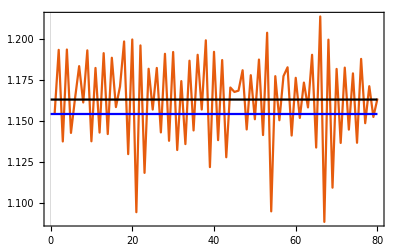

```mathematica
Show[
ListLinePlot[hdata],
ListLinePlot[{{0,Mean[hdata]},{Length[hdata],Mean[hdata]}},PlotStyle->Black],
ListLinePlot[{{0,hinit},{Length[hdata],hinit}},PlotStyle->Blue]
]
```

```mathematica
Mean[hdata]
```

1.16313

```mathematica
Mean[hdata[[-100;;]]]
```

Part::take: Cannot take positions -100 through -1 in {1.15435,1.19335,1.13765,1.19355,1.14285,1.16395,1.18345,1.16135,1.19305,1.13775,1.18235,1.14305,1.19135,1.14215,1.18855,1.15855,1.17105,1.19845,«16»,1.14435,1.19035,1.15705,1.19915,1.12205,1.19215,1.13845,1.18715,1.12805,1.17045,1.16775,1.16855,1.18095,1.14495,1.17795,1.15115,«30»}.

Mean[{1.15435,1.19335,1.13765,1.19355,1.14285,1.16395,1.18345,1.16135,1.19305,1.13775,1.18235,1.14305,1.19135,1.14215,1.18855,1.15855,1.17105,1.19845,1.12995,1.19965,1.09465,1.19605,1.11855,1.18185,1.15705,1.18235,1.14315,1.19095,1.13805,1.19205,1.13245,1.17435,1.13605,1.18675,1.14435,1.19035,1.15705,1.19915,1.12205,1.19215,1.13845,1.18715,1.12805,1.17045,1.16775,1.16855,1.18095,1.14495,1.17795,1.15115,1.18745,1.14155,1.20375,1.09515,1.17735,1.15055,1.17735,1.18275,1.14125,1.17635,1.15195,1.17345,1.15835,1.19035,1.13395,1.21365,1.08875,1.19955,1.10955,1.18175,1.13675,1.18255,1.14485,1.17905,1.13685,1.18785,1.14875,1.17125,1.15255,1.16375}⟦-100;;All⟧]

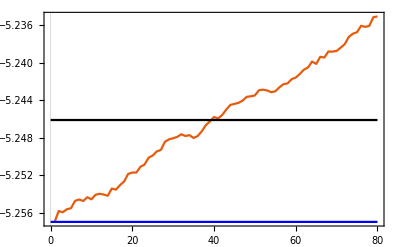

```mathematica
Show[
ListLinePlot[wdata],
ListLinePlot[{{0,Mean[wdata]},{Length[wdata],Mean[wdata]}},PlotStyle->Black],
ListLinePlot[{{0,winit},{Length[wdata],winit}},PlotStyle->Blue]
]
```

```mathematica
Mean[wdata]
```

-5.2461

```mathematica
Mean[wdata[[-100;;]]]
```

Part::take: Cannot take positions -100 through -1 in {-5.25697,-5.25581,-5.25594,-5.25562,-5.25551,-5.25473,-5.25458,-5.25474,-5.25434,-5.25456,-5.25408,-5.25397,-5.25405,-5.25418,-5.25341,-5.25353,«19»,-5.24781,-5.24731,-5.24665,-5.24625,-5.24578,-5.24593,-5.24557,-5.24499,-5.24449,-5.24438,-5.24427,-5.24403,-5.24363,-5.24357,-5.24348,«30»}.

Mean[{-5.25697,-5.25581,-5.25594,-5.25562,-5.25551,-5.25473,-5.25458,-5.25474,-5.25434,-5.25456,-5.25408,-5.25397,-5.25405,-5.25418,-5.25341,-5.25353,-5.25305,-5.25266,-5.25185,-5.25171,-5.2517,-5.25109,-5.25085,-5.25012,-5.24989,-5.24945,-5.24929,-5.24842,-5.24816,-5.24804,-5.2479,-5.24762,-5.24781,-5.24771,-5.24802,-5.24781,-5.24731,-5.24665,-5.24625,-5.24578,-5.24593,-5.24557,-5.24499,-5.24449,-5.24438,-5.24427,-5.24403,-5.24363,-5.24357,-5.24348,-5.24292,-5.24286,-5.24295,-5.24313,-5.24304,-5.24261,-5.24228,-5.24219,-5.24174,-5.24157,-5.24118,-5.24073,-5.24049,-5.23986,-5.24011,-5.23936,-5.23943,-5.23879,-5.2388,-5.23873,-5.23838,-5.238,-5.23722,-5.23689,-5.23673,-5.23605,-5.23616,-5.23606,-5.23513,-5.23505}⟦-100;;All⟧]